{{y[t]→1/(2 √(γ^2-w_n^2) (w^4+4 w^2 γ^2-2 w^2 w_n^2+w_n^4))ⅇ^(-t (γ+√(γ^2-w_n^2))) ((-1+ⅇ^(2 t √(γ^2-w_n^2))) w ((w^2+2 γ^2) Cos[ϕ]-w γ Sin[ϕ])+w ((1+ⅇ^(2 t √(γ^2-w_n^2))) (2 γ Cos[ϕ]+w Sin[ϕ])-2 ⅇ^(t (γ+√(γ^2-w_n^2))) (2 γ Cos[t w+ϕ]+w Sin[t w+ϕ])) √(γ^2-w_n^2)+w_n^2 (-(-1+ⅇ^(2 t √(γ^2-w_n^2))) w Cos[ϕ]+γ Sin[ϕ]+2 ⅇ^(t (γ+√(γ^2-w_n^2))) Sin[t w+ϕ] √(γ^2-w_n^2)-Sin[ϕ] (√(γ^2-w_n^2)+ⅇ^(2 t √(γ^2-w_n^2)) (γ+√(γ^2-w_n^2))))) UnitStep[t]}}

1/(2 √(γ^2-w_n^2) (w^4+4 w^2 γ^2-2 w^2 w_n^2+w_n^4))ⅇ^(-t (γ+√(γ^2-w_n^2))) (Piecewise[{{Indeterminate, t==0}, {0, True}}]) ((-1+ⅇ^(2 t √(γ^2-w_n^2))) w ((w^2+2 γ^2) Cos[ϕ]-w γ Sin[ϕ])+w ((1+ⅇ^(2 t √(γ^2-w_n^2))) (2 γ Cos[ϕ]+w Sin[ϕ])-2 ⅇ^(t (γ+√(γ^2-w_n^2))) (2 γ Cos[t w+ϕ]+w Sin[t w+ϕ])) √(γ^2-w_n^2)+w_n^2 (-(-1+ⅇ^(2 t √(γ^2-w_n^2))) w Cos[ϕ]+γ Sin[ϕ]+2 ⅇ^(t (γ+√(γ^2-w_n^2))) Sin[t w+ϕ] √(γ^2-w_n^2)-Sin[ϕ] (√(γ^2-w_n^2)+ⅇ^(2 t √(γ^2-w_n^2)) (γ+√(γ^2-w_n^2)))))+1/(2 √(γ^2-w_n^2) (w^4+4 w^2 γ^2-2 w^2 w_n^2+w_n^4))ⅇ^(-t (γ+√(γ^2-w_n^2))) (2 ⅇ^(2 t √(γ^2-w_n^2)) w ((w^2+2 γ^2) Cos[ϕ]-w γ Sin[ϕ]) √(γ^2-w_n^2)+w √(γ^2-w_n^2) (-2 ⅇ^(t (γ+√(γ^2-w_n^2))) (w^2 Cos[t w+ϕ]-2 w γ Sin[t w+ϕ])+2 ⅇ^(2 t √(γ^2-w_n^2)) (2 γ Cos[ϕ]+w Sin[ϕ]) √(γ^2-w_n^2)-2 ⅇ^(t (γ+√(γ^2-w_n^2))) (2 γ Cos[t w+ϕ]+w Sin[t w+ϕ]) (γ+√(γ^2-w_n^2)))+w_n^2 (-2 ⅇ^(2 t √(γ^2-w_n^2)) w Cos[ϕ] √(γ^2-w_n^2)+2 ⅇ^(t (γ+√(γ^2-w_n^2))) w Cos[t w+ϕ] √(γ^2-w_n^2)-2 ⅇ^(2 t √(γ^2-w_n^2)) Sin[ϕ] √(γ^2-w_n^2) (γ+√(γ^2-w_n^2))+2 ⅇ^(t (γ+√(γ^2-w_n^2))) Sin[t w+ϕ] √(γ^2-w_n^2) (γ+√(γ^2-w_n^2)))) UnitStep[t]+1/(2 √(γ^2-w_n^2) (w^4+4 w^2 γ^2-2 w^2 w_n^2+w_n^4))ⅇ^(-t (γ+√(γ^2-w_n^2))) (-γ-√(γ^2-w_n^2)) ((-1+ⅇ^(2 t √(γ^2-w_n^2))) w ((w^2+2 γ^2) Cos[ϕ]-w γ Sin[ϕ])+w ((1+ⅇ^(2 t √(γ^2-w_n^2))) (2 γ Cos[ϕ]+w Sin[ϕ])-2 ⅇ^(t (γ+√(γ^2-w_n^2))) (2 γ Cos[t w+ϕ]+w Sin[t w+ϕ])) √(γ^2-w_n^2)+w_n^2 (-(-1+ⅇ^(2 t √(γ^2-w_n^2))) w Cos[ϕ]+γ Sin[ϕ]+2 ⅇ^(t (γ+√(γ^2-w_n^2))) Sin[t w+ϕ] √(γ^2-w_n^2)-Sin[ϕ] (√(γ^2-w_n^2)+ⅇ^(2 t √(γ^2-w_n^2)) (γ+√(γ^2-w_n^2))))) UnitStep[t]

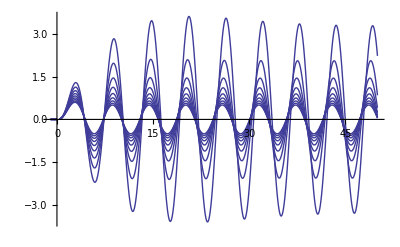

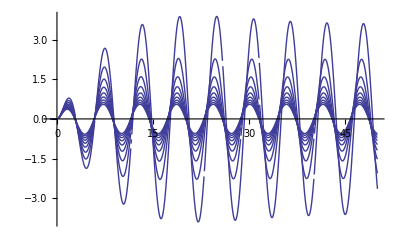

```mathematica
(* Solution of a driven damped harmonic oscillator system
Useful for analytically solving for coil current in a tuned probe *)

(* set initial conditions to zero to get driven / particular solution *)
(* sinusoidal input*)
soln = FullSimplify[DSolve[{y''[t]+2 γ y'[t]+Subscript[w, n]^2 y[t]==UnitStep[t]Sin[w t+ϕ],y[0]==0,y'[0]==0},y[t],t]]
Ic[t_] = y[t]/.soln[[1]];
dIc[t_] =FullSimplify[ D[Ic[t],t]]
Ictab[t_]= Table[Ic[t]/.{γ->0.1j,Subscript[w, n]->1,w->1.1,ϕ->0},{j,1,9}];
dIctab[t_]= Table[dIc[t]/.{γ->0.1j,Subscript[w, n]->1,w->1.1,ϕ->0},{j,1,9}];
Plot[Ictab[t],{t,-1,50}]
Plot[dIctab[t],{t,-1,50}]
```

{{y[tv]→1/(2 √((gamma-wn) (gamma+wn)) (4 gamma^2 w^2+(w^2-wn^2)^2))ⅇ^(-tv (gamma+√(gamma^2-wn^2))) (2 gamma w √((gamma-wn) (gamma+wn)) Cos[phi]+2 ⅇ^(2 tv √(gamma^2-wn^2)) gamma w √((gamma-wn) (gamma+wn)) Cos[phi]-4 ⅇ^(tv (gamma+√(gamma^2-wn^2))) gamma w √((gamma-wn) (gamma+wn)) Cos[phi+tv w]+w^2 √((gamma-wn) (gamma+wn)) Sin[phi]+ⅇ^(2 tv √(gamma^2-wn^2)) w^2 √((gamma-wn) (gamma+wn)) Sin[phi]-wn^2 √((gamma-wn) (gamma+wn)) Sin[phi]-ⅇ^(2 tv √(gamma^2-wn^2)) wn^2 √((gamma-wn) (gamma+wn)) Sin[phi]+(-1+ⅇ^(2 tv √(gamma^2-wn^2))) (w (2 gamma^2+w^2-wn^2) Cos[phi]-gamma (w^2+wn^2) Sin[phi])-2 ⅇ^(tv (gamma+√(gamma^2-wn^2))) w^2 √((gamma-wn) (gamma+wn)) Sin[phi+tv w]+2 ⅇ^(tv (gamma+√(gamma^2-wn^2))) wn^2 √((gamma-wn) (gamma+wn)) Sin[phi+tv w]) UnitStep[tv]}}

Piecewise[{{Indeterminate, tv==0}, {1/(2 √((gamma-wn) (gamma+wn)) (4 gamma^2 w^2+(w^2-wn^2)^2))ⅇ^(-tv (gamma+√(gamma^2-wn^2))) (w (-(1+ⅇ^(2 tv √(gamma^2-wn^2))) √((gamma-wn) (gamma+wn)) (-w^2+wn^2)-(-1+ⅇ^(2 tv √(gamma^2-wn^2))) gamma (w^2+wn^2)) Cos[phi]+2 ⅇ^(tv (gamma+√((gamma-wn) (gamma+wn)))) w √((gamma-wn) (gamma+wn)) (-w^2+wn^2) Cos[phi+tv w]-2 gamma w^2 √((gamma-wn) (gamma+wn)) Sin[phi]-2 ⅇ^(2 tv √(gamma^2-wn^2)) gamma w^2 √((gamma-wn) (gamma+wn)) Sin[phi]+(-1+ⅇ^(2 tv √(gamma^2-wn^2))) (2 gamma^2 w^2-w^2 wn^2+wn^4) Sin[phi]+4 ⅇ^(tv (gamma+√((gamma-wn) (gamma+wn)))) gamma w^2 √((gamma-wn) (gamma+wn)) Sin[phi+tv w]), tv>0}, {0, True}}]

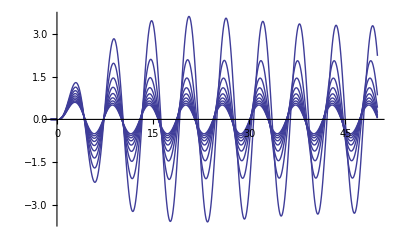

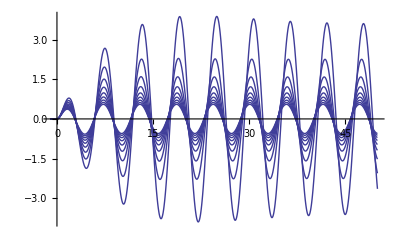

```mathematica
soln = FullSimplify[DSolve[{y''[tv]+2 gamma y'[tv]+wn^2 y[tv]==UnitStep[tv]Sin[w tv+phi],y[0]==0,y'[0]==0},y[tv],tv]]
Ic[tv_] = y[tv]/.soln[[1]];
dIc[tv_] = FullSimplify[D[Ic[tv],tv]]
Ictab[tv_]= Table[Ic[tv]/.{gamma->0.1j,wn->1,w->1.1,phi->0},{j,1,9}];
dIctab[tv_]= Table[dIc[tv]/.{gamma->0.1j,wn->1,w->1.1,phi->0},{j,1,9}];
Plot[Ictab[tv],{tv,-1,50}]
Plot[dIctab[tv],{tv,-1,50}]
```

```mathematica
InputForm[1/(2 √((gamma-wn) (gamma+wn)) (4 gamma^2 w^2+(w^2-wn^2)^2))ⅇ^(-tv (gamma+√(gamma^2-wn^2))) (2 gamma w √((gamma-wn) (gamma+wn)) Cos[phi]+2 ⅇ^(2 tv √(gamma^2-wn^2)) gamma w √((gamma-wn) (gamma+wn)) Cos[phi]-4 ⅇ^(tv (gamma+√(gamma^2-wn^2))) gamma w √((gamma-wn) (gamma+wn)) Cos[phi+tv w]+w^2 √((gamma-wn) (gamma+wn)) Sin[phi]+ⅇ^(2 tv √(gamma^2-wn^2)) w^2 √((gamma-wn) (gamma+wn)) Sin[phi]-wn^2 √((gamma-wn) (gamma+wn)) Sin[phi]-ⅇ^(2 tv √(gamma^2-wn^2)) wn^2 √((gamma-wn) (gamma+wn)) Sin[phi]+(-1+ⅇ^(2 tv √(gamma^2-wn^2))) (w (2 gamma^2+w^2-wn^2) Cos[phi]-gamma (w^2+wn^2) Sin[phi])-2 ⅇ^(tv (gamma+√(gamma^2-wn^2))) w^2 √((gamma-wn) (gamma+wn)) Sin[phi+tv w]+2 ⅇ^(tv (gamma+√(gamma^2-wn^2))) wn^2 √((gamma-wn) (gamma+wn)) Sin[phi+tv w])]
```

(2*gamma*w*Sqrt[(gamma - wn)*(gamma + wn)]*Cos[phi] + 2*E^(2*tv*Sqrt[gamma^2 - wn^2])*gamma*w*Sqrt[(gamma - wn)*(gamma + wn)]*Cos[phi] - 4*E^(tv*(gamma + Sqrt[gamma^2 - wn^2]))*gamma*w*Sqrt[(gamma - wn)*(gamma + wn)]*Cos[phi + tv*w] + 
  w^2*Sqrt[(gamma - wn)*(gamma + wn)]*Sin[phi] + E^(2*tv*Sqrt[gamma^2 - wn^2])*w^2*Sqrt[(gamma - wn)*(gamma + wn)]*Sin[phi] - wn^2*Sqrt[(gamma - wn)*(gamma + wn)]*Sin[phi] - E^(2*tv*Sqrt[gamma^2 - wn^2])*wn^2*Sqrt[(gamma - wn)*(gamma + wn)]*Sin[phi] + 
  (-1 + E^(2*tv*Sqrt[gamma^2 - wn^2]))*(w*(2*gamma^2 + w^2 - wn^2)*Cos[phi] - gamma*(w^2 + wn^2)*Sin[phi]) - 2*E^(tv*(gamma + Sqrt[gamma^2 - wn^2]))*w^2*Sqrt[(gamma - wn)*(gamma + wn)]*Sin[phi + tv*w] + 
  2*E^(tv*(gamma + Sqrt[gamma^2 - wn^2]))*wn^2*Sqrt[(gamma - wn)*(gamma + wn)]*Sin[phi + tv*w])/(2*E^(tv*(gamma + Sqrt[gamma^2 - wn^2]))*Sqrt[(gamma - wn)*(gamma + wn)]*(4*gamma^2*w^2 + (w^2 - wn^2)^2))

```mathematica
InputForm[1/(2 √((gamma-wn) (gamma+wn)) (4 gamma^2 w^2+(w^2-wn^2)^2))ⅇ^(-tv (gamma+√(gamma^2-wn^2))) (w (-(1+ⅇ^(2 tv √(gamma^2-wn^2))) √((gamma-wn) (gamma+wn)) (-w^2+wn^2)-(-1+ⅇ^(2 tv √(gamma^2-wn^2))) gamma (w^2+wn^2)) Cos[phi]+2 ⅇ^(tv (gamma+√((gamma-wn) (gamma+wn)))) w √((gamma-wn) (gamma+wn)) (-w^2+wn^2) Cos[phi+tv w]-2 gamma w^2 √((gamma-wn) (gamma+wn)) Sin[phi]-2 ⅇ^(2 tv √(gamma^2-wn^2)) gamma w^2 √((gamma-wn) (gamma+wn)) Sin[phi]+(-1+ⅇ^(2 tv √(gamma^2-wn^2))) (2 gamma^2 w^2-w^2 wn^2+wn^4) Sin[phi]+4 ⅇ^(tv (gamma+√((gamma-wn) (gamma+wn)))) gamma w^2 √((gamma-wn) (gamma+wn)) Sin[phi+tv w])]
```

```mathematica
(w*((-1 - E^(2*tv*Sqrt[gamma^2 - wn^2]))*Sqrt[(gamma - wn)*(gamma + wn)]*(-w^2 + wn^2) - (-1 + E^(2*tv*Sqrt[gamma^2 - wn^2]))*gamma*(w^2 + wn^2))*Cos[phi] + 
  2*E^(tv*(gamma + Sqrt[(gamma - wn)*(gamma + wn)]))*w*Sqrt[(gamma - wn)*(gamma + wn)]*(-w^2 + wn^2)*Cos[phi + tv*w] - 2*gamma*w^2*Sqrt[(gamma - wn)*(gamma + wn)]*Sin[phi] - 
  2*E^(2*tv*Sqrt[gamma^2 - wn^2])*gamma*w^2*Sqrt[(gamma - wn)*(gamma + wn)]*Sin[phi] + (-1 + E^(2*tv*Sqrt[gamma^2 - wn^2]))*(2*gamma^2*w^2 - w^2*wn^2 + wn^4)*Sin[phi] + 
  4*E^(tv*(gamma + Sqrt[(gamma - wn)*(gamma + wn)]))*gamma*w^2*Sqrt[(gamma - wn)*(gamma + wn)]*Sin[phi + tv*w])/(2*E^(tv*(gamma + Sqrt[gamma^2 - wn^2]))*Sqrt[(gamma - wn)*(gamma + wn)]*(4*gamma^2*w^2 + (w^2 - wn^2)^2))
```

{{y[t]→(ⅇ^(ⅈ ϕ-t (γ+√(γ^2-ω_n^2))) ((-1+ⅇ^(2 t √(γ^2-ω_n^2))) γ+ⅈ (-1+ⅇ^(2 t √(γ^2-ω_n^2))) ω+(1+ⅇ^(2 t √(γ^2-ω_n^2))-2 ⅇ^(t (γ+ⅈ ω+√(γ^2-ω_n^2)))) √(γ^2-ω_n^2)) UnitStep[t])/(2 √(γ^2-ω_n^2) (ω (-2 ⅈ γ+ω)-ω_n^2))}}

Piecewise[{{Indeterminate, t==0}, {-(ⅇ^(ⅈ ϕ-t (γ+√(γ^2-ω_n^2))) (ⅈ (-1+ⅇ^(2 t √(γ^2-ω_n^2))) ω_n^2+ω (γ-ⅇ^(2 t √(γ^2-ω_n^2)) γ+(1+ⅇ^(2 t √(γ^2-ω_n^2))-2 ⅇ^(t (γ+ⅈ ω+√(γ^2-ω_n^2)))) √(γ^2-ω_n^2))))/(2 √(γ^2-ω_n^2) ((2 γ+ⅈ ω) ω-ⅈ ω_n^2)), t>0}, {0, True}}]

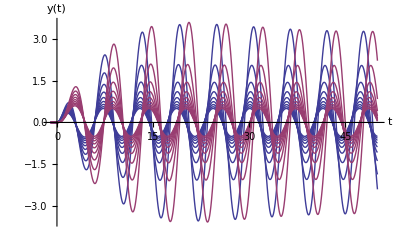

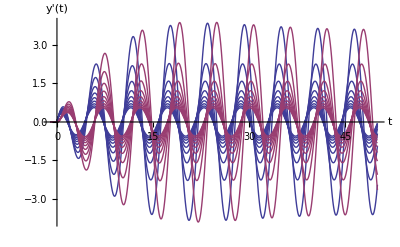

```mathematica
(* exponential input*)
soln = FullSimplify[DSolve[{y''[t]+(2γ)y'[t]+Subscript[ω, n]^2 y[t]==UnitStep[t] ⅇ^(ⅈ(ω t+ϕ)),y[0]==0,y'[0]==0},y[t],t]]
Ic[t_] = y[t]/.soln[[1]];
dIc[t_] = FullSimplify[D[Ic[t],t]]
Ictab[t_]= Table[Ic[t]/.{γ->0.1j,Subscript[ω, n]->1,ω->1.1,ϕ->0},{j,1,9}];
dIctab[t_]= Table[dIc[t]/.{γ->0.1j,Subscript[ω, n]->1,ω->1.1,ϕ->0},{j,1,9}];
Plot[{Re[Ictab[t]],Im[Ictab[t]]},{t,-1,50},AxesLabel->{t,y[t]}]
Plot[{Re[dIctab[t]],Im[dIctab[t]]},{t,-1,50},AxesLabel->{t,y'[t]}]
```

{{y[tv]→(ⅇ^(ⅈ phi-tv (gamma+√((gamma-wn) (gamma+wn)))) ((-1+ⅇ^(2 tv √(gamma^2-wn^2))) gamma+ⅈ (-1+ⅇ^(2 tv √(gamma^2-wn^2))) w+(1+ⅇ^(2 tv √(gamma^2-wn^2))-2 ⅇ^(tv (gamma+ⅈ w+√((gamma-wn) (gamma+wn))))) √((gamma-wn) (gamma+wn))) UnitStep[tv])/(2 √((gamma-wn) (gamma+wn)) (-2 ⅈ gamma w+w^2-wn^2))}}

Piecewise[{{Indeterminate, tv==0}, {(ⅇ^(ⅈ phi-tv (gamma+√(gamma^2-wn^2))) ((-1+ⅇ^(2 tv √(gamma^2-wn^2))) gamma w-ⅈ (-1+ⅇ^(2 tv √(gamma^2-wn^2))) wn^2-(1+ⅇ^(2 tv √(gamma^2-wn^2))-2 ⅇ^(tv (gamma+ⅈ w+√(gamma^2-wn^2)))) w √(gamma^2-wn^2)))/(2 √((gamma-wn) (gamma+wn)) (2 gamma w+ⅈ (w-wn) (w+wn))), tv>0}, {0, True}}]

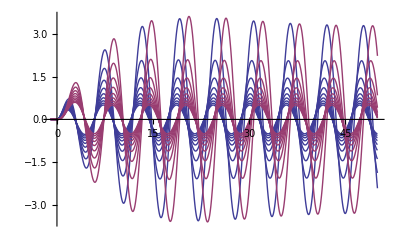

```mathematica
(* exponential input*)
soln = FullSimplify[DSolve[{y''[tv]+2 gamma y'[tv]+wn^2 y[tv]==UnitStep[tv] ⅇ^(ⅈ(w tv+phi)),y[0]==0,y'[0]==0},y[tv],tv]]
Ic[tv_] = y[tv]/.soln[[1]];
dIc[tv_] = FullSimplify[D[Ic[tv],tv]]
Ictab[tv_]= Table[Ic[tv]/.{gamma->0.1j,wn->1,w->1.1,phi->0},{j,1,9}];
dIctab[tv_]= Table[dIc[tv]/.{gamma->0.1j,wn->1,w->1.1,phi->0},{j,1,9}];
Plot[{Re[Ictab[tv]],Im[Ictab[tv]]},{tv,-1,50}]
Plot[{Re[dIctab[tv]],Im[dIctab[tv]]},{tv,-1,50}]
```

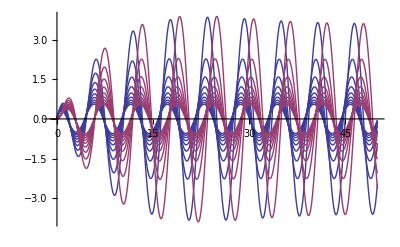

```mathematica
InputForm[(ⅇ^(ⅈ phi-tv (gamma+√((gamma-wn) (gamma+wn)))) ((-1+ⅇ^(2 tv √(gamma^2-wn^2))) gamma+ⅈ (-1+ⅇ^(2 tv √(gamma^2-wn^2))) w+(1+ⅇ^(2 tv √(gamma^2-wn^2))-2 ⅇ^(tv (gamma+ⅈ w+√((gamma-wn) (gamma+wn))))) √((gamma-wn) (gamma+wn))) UnitStep[tv])/(2 √((gamma-wn) (gamma+wn)) (-2 ⅈ gamma w+w^2-wn^2))]
```

(E^(I*phi - tv*(gamma + Sqrt[(gamma - wn)*(gamma + wn)]))*((-1 + E^(2*tv*Sqrt[gamma^2 - wn^2]))*gamma + I*(-1 + E^(2*tv*Sqrt[gamma^2 - wn^2]))*w + (1 + E^(2*tv*Sqrt[gamma^2 - wn^2]) - 2*E^(tv*(gamma + I*w + Sqrt[(gamma - wn)*(gamma + wn)])))*
    Sqrt[(gamma - wn)*(gamma + wn)])*UnitStep[tv])/(2*Sqrt[(gamma - wn)*(gamma + wn)]*((-2*I)*gamma*w + w^2 - wn^2))

```mathematica
InputForm[(ⅇ^(ⅈ phi-tv (gamma+√(gamma^2-wn^2))) ((-1+ⅇ^(2 tv √(gamma^2-wn^2))) gamma w-ⅈ (-1+ⅇ^(2 tv √(gamma^2-wn^2))) wn^2-(1+ⅇ^(2 tv √(gamma^2-wn^2))-2 ⅇ^(tv (gamma+ⅈ w+√(gamma^2-wn^2)))) w √(gamma^2-wn^2)))/(2 √((gamma-wn) (gamma+wn)) (2 gamma w+ⅈ (w-wn) (w+wn)))]
```

(E^(I*phi - tv*(gamma + Sqrt[gamma^2 - wn^2]))*((-1 + E^(2*tv*Sqrt[gamma^2 - wn^2]))*gamma*w - I*(-1 + E^(2*tv*Sqrt[gamma^2 - wn^2]))*wn^2 - (1 + E^(2*tv*Sqrt[gamma^2 - wn^2]) - 2*E^(tv*(gamma + I*w + Sqrt[gamma^2 - wn^2])))*w*Sqrt[gamma^2 - wn^2]))/
 (2*Sqrt[(gamma - wn)*(gamma + wn)]*(2*gamma*w + I*(w - wn)*(w + wn)))

```mathematica
(* First order equation *)
```

{{y[t]→(ⅇ^(-t/τ+ⅈ ϕ) (-1+ⅇ^(t (1/τ+ⅈ ω))) τ UnitStep[t])/(1+ⅈ τ ω)}}

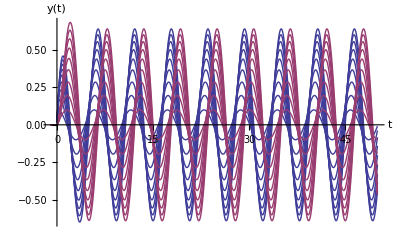

```mathematica
soln = FullSimplify[DSolve[{y'[t]+ y[t]/τ==UnitStep[t] ⅇ^(ⅈ(ω t+ϕ)),y[0]==0},y[t],t]]
Ic[t_] = y[t]/.soln[[1]];
Ictab[t_]= Table[Ic[t]/.{τ->0.1j,ω->1.1,ϕ->0},{j,1,9}];
Plot[{Re[Ictab[t]],Im[Ictab[t]]},{t,-1,50},AxesLabel->{t,y[t]}]
```

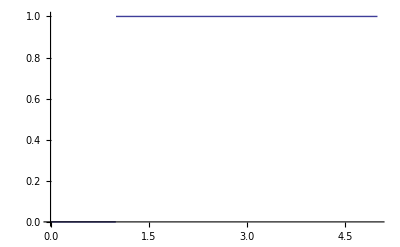

```mathematica
Plot[(UnitStep[t-1]-UnitStep[-1]),{t,0,5}]
```

{{y[t]→(ⅈ ⅇ^(-t/τ+ⅈ ϕ) τ (-ⅇ^(t (1/τ+ⅈ ω)) UnitStep[t-T]+ⅇ^(T (1/τ+ⅈ ω)) (UnitStep[t-T]-UnitStep[-T])+UnitStep[-T]))/(-ⅈ+τ ω)}}

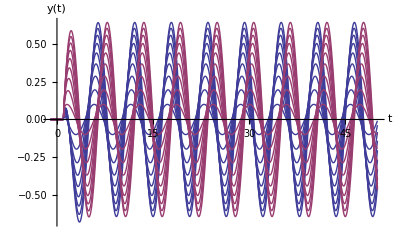

```mathematica
soln = FullSimplify[DSolve[{y'[t]+ y[t]/τ==UnitStep[t-T] ⅇ^(ⅈ(ω t+ϕ)),y[0]==0},y[t],t]]
Ic[t_] = y[t]/.soln[[1]];
Ictab[t_]= Table[Ic[t]/.{τ->0.1j,ω->1.1,ϕ->0,T->1},{j,1,9}];
Plot[{Re[Ictab[t]],Im[Ictab[t]]},{t,-1,50},AxesLabel->{t,y[t]}]
```

```mathematica
Inverse[({{1, 1}, {l1, l2}})]
```

{{l2/(-l1+l2),-1/(-l1+l2)},{-l1/(-l1+l2),1/(-l1+l2)}}